```mathematica
ClearAll["Global`*"]
```

## Import Data

```mathematica
(*task=2; (* 1 for protest; 2 for mass shooting *)*)

data0a=Import[StringJoin[NotebookDirectory[],"2a - analysis - Count Love.xlsx"]]
data0b=Import[StringJoin[NotebookDirectory[],"2b - analysis - MST 2013 - 2018.xlsx"]]

(* first column is data: 1900/1/1 is 1 *)
```

{{{43281.,Lexington, KY,25000.,Civil Rights (Pride),1.,FayetteCounty,Kentucky,38.0406,-84.5037,0.},9938,{42756.,Deming, NM,47.,Civil Rights (Women's March),1.,LunaCounty,NewMexico,32.2687,-107.759,0.}}}
 |  |  |  |

{{{43281.,Jersey City,0.,5.,,HudsonCounty,NewJersey,40.7114,-74.0648,1.},{43280.,Ashburn,0.,8.,,TurnerCounty,Georgia,31.7092,-83.6524,1.},2132,{41275.,McKeesport,0.,4.,,AlleghenyCounty,Pennsylvania,40.3419,-79.845,1.},{41275.,Sacramento,2.,3.,,SacramentoCounty,California,38.5666,-121.469,1.}}}
 |  |  |  |

## Data Selection and Cleaning

```mathematica
(* select some data only; remove selection column *)
{{xMin,xMax},{yMin,yMax}}={{-130,-65},{25,50}}(*{{-170,-65},{25,70}}*);
msAdj=1; (* Microsoft Excel mistaken let 1900/2/29 exist,which shouldn't *)
dateFilter=First@DateDifference[DateObject[{1900, 1, 1}],DateObject[{2017, 3, 3}]]+1+msAdj;

filter[data0_]:=
(
d1=First@data0;


d1=Select[d1,#[[-1]]==1&];

d1=Drop[d1,None,{-1}];

d1=Select[d1,And[yMin<=#[[-2]]≤yMax,xMin<=#[[-1]]≤xMax]&];

(* remove cases with location N/A *)
d1=Select[d1,#[[-1]]≠"Failure"&];

(* filter out old dates *)

d1=Select[d1,#[[1]]>=dateFilter&];

firstdate=Min@d1[[All,1]];
firstdateD=DateObject[{1900, 1, 1}]+Quantity[firstdate-1-msAdj,"Days"];

(* Delete Duplicate *)
d1=SortBy[d1,{-#[[1]],-#[[3]]}&];
d1=DeleteDuplicatesBy[d1,#[[{1,-2,-1}]]&];

(*Output*)
{d1,firstdate,firstdateD}
);

{data1,firstdate,firstdateD}=filter[data0a];
```

```mathematica
(*scale filtering for MST*)

scaleTime1=175; (* justified in "0.2 - counties distance.nb" *)

data1b=First@filter[data0b];
data2b=MapAt[(#-firstdate)/365*scaleTime1&,data1b,{All,1}];

kScaleFilter=5;
wScaleFilter=10;
data1b=Select[data2b,Or[#[[3]]≥kScaleFilter,#[[4]]≥wScaleFilter]&];

data2bPurple=Select[data2b,And[#[[3]]≥kScaleFilter,#[[4]]≥wScaleFilter]&];
data2bRed=Complement[Select[data2b,#[[3]]≥kScaleFilter&],data2bPurple];
data2bBlue=Complement[Select[data2b,#[[4]]≥wScaleFilter&],data2bPurple];
data2bCat={data2bPurple,data2bRed,data2bBlue};
```

## Clustering

```mathematica
(* rescaling *)
(* Do Clustering *)

nStart=1;
nEnd=Length[data1]; (* or smaller; all = 6077*)

nCts=Automatic;

(* created data2 = rescaled(data1)  *)
data2=MapAt[(#-firstdate)/365*scaleTime1&,data1,{All,1}];

(*data2[[All,1]]=data2[[All,1]]*scaleTime1;*)
{t,cts}=Timing@FindClusters[data2[[nStart;;nEnd,{1,-2,-1}]]->data2[[nStart;;nEnd]],nCts,DistanceFunction->EuclideanDistance];
 t

(* {t,cts}=Timing@FindClusters[data2[[nStart;;nEnd,{1,-2,-1}]]->data2[[nStart;;nEnd]],DistanceFunction->EuclideanDistance,Method->"Agglomerate"] *)
(* {t,cts}=Timing@FindClusters[data2[[nStart;;nEnd,{1,-2,-1}]]->data2[[nStart;;nEnd]],nCts,CriterionFunction->"CalinskiHarabasz"] *)
(*data2[[All,1]]=data2[[All,1]]/scaleTime1;*)

n=Length[cts]
```

5.03125

9

## Plotting

```mathematica
(* create the image of Geo Map *)

yManualAdj=0;

g1=(GeoPosition[{yMin+yManualAdj,#}]&/@Range[xMin,xMax,5]);
g2=(GeoPosition[{yMax+yManualAdj,#}]&/@Range[xMax,xMin,-5]);
img=Lighter@GeoGraphics[Polygon@Join[g1,g2],GeoProjection->"CylindricalEqualArea",GeoRangePadding->None];
```

```mathematica
(* year adj*)
MaxTimeD=DateObject[{2018,6,30}];
MaxTime=N@(First@DateDifference[firstdateD,MaxTimeD])*scaleTime1/365;

ctsSel=cts[[All,All,{-1,-2,1}]];
plotRange1={{xMin,xMax},{yMin,yMax},{0,MaxTime}};
boxRatios1={1.2,0.7,2};

slicesB={0,MaxTime}; 
slicesN={0,0.721,0.778,0.798,0.855,1}*MaxTime; 
colCts=ColorData[97]/@Range[n];

stringTick={"Mass shooting in Parkland","School Walkout","March for Our Lives","19th anniversary of Columbine High School massacre"};
timetick1=Table[{n,DateString[firstdateD+Quantity[n/scaleTime1,"Years"],{"Month","/","Day","/","YearShort"}]},{n,slicesN}]; 
legend1=Column@Reverse@MapThread[StringJoin[ToString@#1," - ",#2]&,{timetick1[[2;;-2,2]],stringTick}];

(* clustering plots for protest *)
plot1B=Legended[Plot3D[Drop[slicesB,-1],{x,xMin,xMax},{y,yMin,yMax},PlotRange->plotRange1,Ticks->{Automatic,Automatic,timetick1},BoxRatios->boxRatios1,PlotStyle->Texture[img]],legend1];
plot1N=Plot3D[Drop[slicesN,-1],{x,xMin,xMax},{y,yMin,yMax},PlotStyle->Texture[img]];
plot2=ListPointPlot3D[ctsSel,PlotRange->plotRange1,Ticks->{Automatic,Automatic,timetick1},BoxRatios->boxRatios1];
plot3=Table[{HighlightMesh[ConvexHullMesh[ctsSel[[i]]],Style[2,colCts[[i]],Opacity[0.5]]]},{i,n}];
plot4=Graphics3D[{Transpose[{colCts,Point/@ctsSel}],Opacity[0.25],Transpose[{colCts,BoundingRegion[#,"FastEllipsoid"]&/@ctsSel}]}];
```

```mathematica
(* Bubble Chart for MST *)
cef[br_: {1,1,1}][cedf_: "Bubble3D"]:=Scale[ChartElementData[cedf][##],1/br]&;
cef2[br_: {1,1,1},pr_]:=(dPr=Flatten@(Differences/@pr);
Scale[ChartElementData["Bubble3D"][##],MapThread[Times,{1/br,dPr/Min[dPr]}]]&);


data1b=MapAt[(#-firstdate)/365*scaleTime1&,data1b,{All,1}];
bChart=BubbleChart3D[data2bCat[[All,All,{-1,-2,1,3}]],BoxRatios->boxRatios1,ChartElementFunction->cef[boxRatios1][]]
bChart2=BubbleChart3D[data2bCat[[All,All,{-1,-2,1,3}]]]
bChart=BubbleChart3D[data2bCat[[All,All,{-1,-2,1,3}]],BoxRatios->boxRatios1,ChartElementFunction->cef[boxRatios1][],ChartStyle->{Red,Yellow,Black}]


(*(*test*)
cef3[br_: {1,1,1},pr_]:=(dPr=Flatten@(Differences/@pr);Scale[ChartElementData["Bubble3D"][##],MapThread[Times,{1/br,dPr/Min[dPr]}]]&);
pr2={{-130,-65},{25,50},{0,232}};
bchart3b=BubbleChart3D[pts3,ImageSize->200,BoxRatios->br1,ChartElementFunction->cef3[br1,pr2],PlotRange->pr2]*)
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
(* combine plots *)
assoPlot=<|
"Protest"->Show[{plot1B,plot2},ViewPoint->{-1.3,-2.4,2}],
"Slices"->Show[{plot1B,plot1N,plot2}],
"Clusters"->Show[{plot1B,plot2,plot3}],
"Ellipsoid"->Show[{plot1B,plot4}],
"Protest and Shooting 1"->Show[{plot1B,plot2,plot3,bChart}],
"Protest and Shooting 2"->Show[{plot1B,plot2,plot3,bChart2}]
|>;

Manipulate[assoPlot[type],{type,Keys@assoPlot,ControlType->SetterBar},SaveDefinitions->True]
```

## Graph

```mathematica
IGMeshGraph[mesh_]:=Graph[Range@MeshCellCount[mesh,0],MeshCells[mesh,1][[All,1]],EdgeWeight->PropertyValue[{mesh,1},MeshCellMeasure],VertexCoordinates->MeshCoordinates[mesh],PlotTheme->"Default"];
f[{p_,q_}]:=Sqrt[p^2+q^2];

plot5All=nAllJ=statEdgeVecAllJ=corrEdgeVecAllJ=lambdasAllJ=ctsSelAllJλ=scaleGrowthAllJ={};

(*** diffussion analysis ***)

 For[j=1,j≤n,j++, (* select cluster *)

(* create tree of the cluster *)

ctsSelJ=ctsSel[[j]];

graph=IGMeshGraph@DelaunayMesh[ctsSelJ];
plot5=FindSpanningTree[graph,VertexCoordinates->GraphEmbedding@graph,EdgeShapeFunction->"Line",EdgeStyle->{Thick,Black},VertexSize->Tiny,VertexStyle->Black,PlotTheme->"Default"];
plot5All=Append[plot5All,plot5];

nJ=VertexCount[plot5];
nAllJ=Append[nAllJ,nJ];

vtxCood=PropertyValue[plot5,VertexCoordinates];

(*** Edges Analysis ***)

edges=EdgeList[plot5];

(* edgeVectors = {combining Δlat and Δlong, Δtime} *)
edgeVectors=Table[vtxDiff=vtxCood[[edges[[n,1]]]]-vtxCood[[edges[[n,2]]]];{f[vtxDiff[[1;;2]]],Abs@vtxDiff[[3]]},{n,1,Length@edges}];

(* jump statistic *)
statEdge=Table[#@edgeVectors[[All,i]]&/@{Mean,StandardDeviation,Quantile[#,{1/4,1/2,3/4}]&},{i,1,2}];
statEdgeVecAllJ=Append[statEdgeVecAllJ,statEdge];

(* deg-time correlation *)
corrEdge=Correlation@edgeVectors;
corrEdgeVecAllJ=Append[corrEdgeVecAllJ,corrEdge[[1,2]]];

(* Gamma Distribution Modeling *)
distml=Table[EstimatedDistribution[edgeVectors[[All,i]],ExponentialDistribution[λ]],{i,1,2}];
{λ1,λ2}=1/Mean/@distml;
lambdasAllJ=Append[lambdasAllJ,{λ1,λ2}];

ctsSelJλ=ArrayFlatten[{{ctsSelJ,ConstantArray[{λ1,λ2,λ1*λ2},nJ]}}];
ctsSelAllJλ=Append[ctsSelAllJλ,ctsSelJλ];

(*** Study expected growth of scale; weight = log(scale) ***)

vtxScale=cts[[j]][[All,3]];

ratioVectors1=Table[
vtx1=edges[[n,1]];
vtx2=edges[[n,2]];
If[Or[vtxScale[[vtx1]]=="---",vtxScale[[vtx2]]=="---",vtxCood[[vtx1,3]]==vtxCood[[vtx2,3]]],
"---",
(vtxScale[[vtx1]]/vtxScale[[vtx2]])^-Order[vtxCood[[vtx1,3]],vtxCood[[vtx2,3]]]
]
,{n,1,Length@edges}];

scaleGrowthKnown=Exp@N@Mean@Log@Select[ratioVectors1,#≠"---"&];
scaleGrowthAllJ=Append[scaleGrowthAllJ,scaleGrowthKnown];

]
```

```mathematica
Manipulate[Legended[Show[{plot1B,plot5All[[cluster]]},ViewPoint->{0.5,-2.4,0}],
Column[{{"#(Pts)",nAllJ[[cluster]]},{Column@{"ΔDeg Stat","Δt Stat"},statEdgeVecAllJ[[cluster]]},{"corr",corrEdgeVecAllJ[[cluster]]},{"λ1, λ2",lambdasAllJ[[cluster]]},{"Scale Growth",scaleGrowthAllJ[[cluster]]}}]
],{cluster,Range@n,ControlType->SetterBar},SaveDefinitions->True]

ctsSelAllJλ=Flatten[ctsSelAllJλ,1];
nAllJ//Column
statEdgeVecAllJ//Column
corrEdgeVecAllJ//Column
lambdasAllJ//Column
scaleGrowthAllJ//Column
```

52
141
287
245
1175
383
189
40
123

{{2.22204,2.0452,{0.396058,1.66916,3.2097}},{1.40075,1.98806,{0.,0.479452,2.39726}}}
{{0.830122,1.64868,{0.0418605,0.0994137,0.595425}},{0.243151,1.09498,{0.,0.,0.}}}
{{0.561208,0.783339,{0.0602293,0.207538,0.806146}},{0.187757,0.841598,{0.,0.,0.}}}
{{0.897818,0.948294,{0.0571824,0.617575,1.56779}},{0.178812,0.857373,{0.,0.,0.}}}
{{0.353786,0.432586,{0.0701199,0.170097,0.481981}},{0.0575833,0.306084,{0.,0.,0.}}}
{{0.312696,0.457872,{0.044539,0.122852,0.377818}},{0.0539697,0.356088,{0.,0.,0.}}}
{{0.474526,0.914775,{0.0590134,0.149347,0.41722}},{0.331536,0.867437,{0.,0.,0.479452}}}
{{2.16411,2.42202,{0.0623882,0.997881,3.57776}},{2.34809,5.86773,{0.,0.479452,1.43836}}}
{{2.12242,3.28509,{0.309132,0.992573,1.77932}},{2.20076,4.39198,{0.,0.958904,1.43836}}}

0.0258141
0.331859
0.283679
0.016055
0.180932
-0.0275836
0.256469
0.385887
0.687751

{0.450037,0.713902}
{1.20464,4.11268}
{1.78187,5.32602}
{1.11381,5.59246}
{2.82657,17.3662}
{3.198,18.5289}
{2.10737,3.01626}
{0.462083,0.425879}
{0.471161,0.454388}

1.52381
0.53455
1.29542
2.69841
1.29782
1.39158
1.4108
1.20497
1.65653

## Prediction

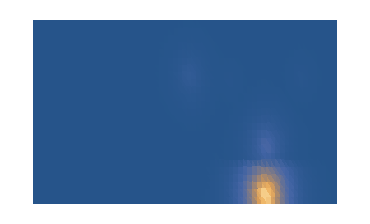

-Graphics-

```mathematica
(* Find nearest points towards the surface-tNow *) 

tNow=Ceiling@MaxTime+0;

precision=1;

tNowSurface=Flatten[Outer[{#1,#2,tNow}&,Range[xMin,xMax,precision],Range[yMin,yMax,precision]],1]; (* for step = 5 : size = 22*10 *)

nearestPtsIdx=Flatten[Nearest[ctsSelAllJλ[[All,1;;3]]->"Index"]/@tNowSurface,1];

nearestPtsCood=ctsSelAllJλ[[#,1;;3]]&/@nearestPtsIdx;
chosenλ=ctsSelAllJλ[[#,4;;5]]&/@nearestPtsIdx;
chosenCoef=ctsSelAllJλ[[#,6]]&/@nearestPtsIdx;

dist=MapThread[{f[#1[[1;;2]]-#2[[1;;2]]],Abs[#1[[3]]-#2[[3]]]}&,{tNowSurface,nearestPtsCood}];
pdfAdj=Exp@-MapThread[#1.#2&,{dist,chosenλ}];
pdfAdj=MapThread[#1*#2&,{pdfAdj,chosenCoef}];

valueSurface=ConstantArray[0,Dimensions@tNowSurface];
valueSurface[[All,1;;2]]=tNowSurface[[All,1;;2]];
valueSurface[[All,3]]=pdfAdj;

img2=ImageResize[img,{370,224}];
plot6=ListDensityPlot[valueSurface,AspectRatio->ImageAspectRatio@img2,PlotRangePadding->0,PlotRange->All,ImageSize->ImageDimensions[img2],Axes->False,Frame->None]
ImageAdd[ImageMultiply[plot6,0.5],ImageMultiply[img2,0.5]]
```